```mathematica
Import["/home/jadeleon/Documents/quantum_chaotic_channels/ja_files/mean_level_spacing_ratio.csv"][[1]]
```

{h_z/h_x,J/h_x,<r_n>}

```mathematica
r=ToExpression[Import["/home/jadeleon/Documents/quantum_chaotic_channels/ja_files/mean_level_spacing_ratio.csv"][[2;;]]];
```

```mathematica
r//Dimensions
```

{90000,3}

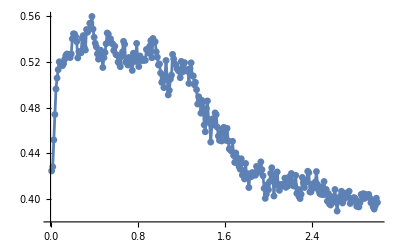

```mathematica
ListPlot[Sort[Select[r,#[[2]]==1&][[All,{1,3}]]],
Joined->True,
PlotMarkers->{Automatic,7}
]
```

```mathematica
rCharly=ToExpression[Import["/home/jadeleon/Documents/quantum_chaotic_channels/rs_mat_python.csv"]];
```

```mathematica
Select[rCharly,#[[2]]=&]
```

```mathematica
(3./40)
```

0.075

```mathematica
Range[0,3,0.075]
```

{0.,0.075,0.15,0.225,0.3,0.375,0.45,0.525,0.6,0.675,0.75,0.825,0.9,0.975,1.05,1.125,1.2,1.275,1.35,1.425,1.5,1.575,1.65,1.725,1.8,1.875,1.95,2.025,2.1,2.175,2.25,2.325,2.4,2.475,2.55,2.625,2.7,2.775,2.85,2.925,3.}

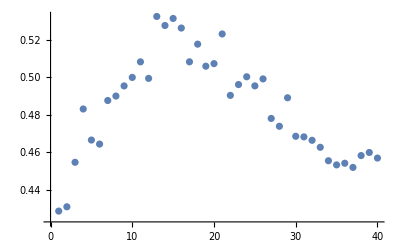

```mathematica
ListPlot[Transpose[rCharly][[13]]]
```